# Пререшаване - Вариант 3, Задача 1, фак. номер 2001261003

a = 0, b = 3

```mathematica
f[x_]:=  (-90Cos[x] + x^3  + 23)/(5 - x^2)
```

```mathematica
f[x]
```

(23+x^3-90 Cos[x])/(5-x^2)

## А) Да се намери общият брой на корените на уравнението

### Визуализация на функцията

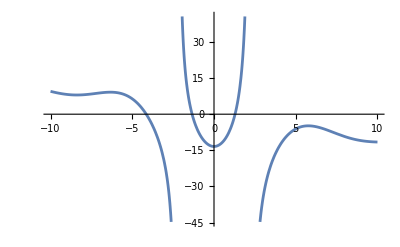

```mathematica
Plot[f[x],{x,-10,10}]
```

Отговор: Уравнението има 3 реални корена, защото графиката на функцията пресича 3 пъти абсцисната ос.

## Б) Да се локализира най-малкият корен

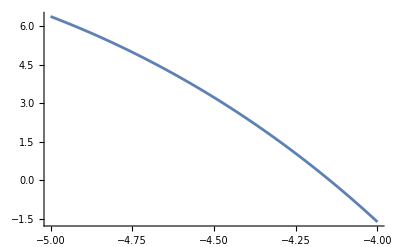

```mathematica
Plot[f[x],{x,-5,-4}]
```

```mathematica
f[-5.]
```

6.37648

```mathematica
f[-4.]
```

-1.62072

Извод:
(1) Функцията f(x) е непрекъсната, защото е сума от непрекъснати функции (полином и косинус).
(2) f(-5) = 6.3764... > 0
       f(-4) = -1.6207... < 0
       => Функцията има различни знаци в двата края на разглеждания интервал [-5; -4].
       От (1) и (2) следва, че функцията има поне един корен в разглеждания интервал [-5; -4].

## В) Да се направят 4 итерации по метода на разполовяването

```mathematica
f[x_]:=  (-90Cos[x] + x^3  + 23)/(5 - x^2)
a = -5.;
b = -4.;
For[n = 0, n <=4 , n++, 
Print["n = ",n, " a_n = ",a, " b_n = ",b, " m_n = ",m =  (a + b)/2  ,  " f(m_n) = ",f[m], " ε_n = ", (b - a)/2];
If[f[m] > 0, b = m, a = m]
]
```

n = 0 a_n = -5. b_n = -4. m_n = -4.5 f(m_n) = 3.22317 ε_n = 0.5

n = 1 a_n = -5. b_n = -4.5 m_n = -4.75 f(m_n) = 4.9854 ε_n = 0.25

n = 2 a_n = -5. b_n = -4.75 m_n = -4.875 f(m_n) = 5.72472 ε_n = 0.125

n = 3 a_n = -5. b_n = -4.875 m_n = -4.9375 f(m_n) = 6.06124 ε_n = 0.0625

n = 4 a_n = -5. b_n = -4.9375 m_n = -4.96875 f(m_n) = 6.22148 ε_n = 0.03125

## г) Посочете достигнатото приближение и с каква точност е то.

Отговор: На четвъртата итерация приближеното решение е -4.96875 с грешка 0.03125.

## д) Колко итерации биха били нужни за достигане на точност ε = 10^-6 за същия интервал?

```mathematica
Log2[(-4+5)/0.000001]-1
```

18.9316

Отговор: Най-малкото цяло число, което е по-голямо от 18.9316 е 19. Следователно са необходими минимум 19 итерации за достигане на исканата точност 10^-6.

```mathematica
f[x_]:=(-90Cos[x] + x^3  + 23)/(5 - x^2)
a = -5.;
b = -4.;
epszad = 0.000001;
eps = 10; (*произволна стойност по-голяма от предварително зададената грешка*)
For[n = 0, eps>epszad, n++,
Print["n = ",n, " a = ",SetPrecision[a,12], " b = ",SetPrecision[b,12], " m = ",SetPrecision[m = (a+b)/2,12], " f(m) = ",f[m], " ε = ",eps =(b-a)/2];
If[f[m]>0,a=m,b=m]
]
```

n = 0 a = -5. b = -4. m = -4.5 f(m) = 3.22317 ε = 0.5

n = 1 a = -4.5 b = -4. m = -4.25 f(m) = 1.04251 ε = 0.25

n = 2 a = -4.25 b = -4. m = -4.125 f(m) = -0.223676 ε = 0.125

n = 3 a = -4.25 b = -4.125 m = -4.1875 f(m) = 0.42504 ε = 0.0625

n = 4 a = -4.1875 b = -4.125 m = -4.15625 f(m) = 0.104673 ε = 0.03125

n = 5 a = -4.15625 b = -4.125 m = -4.140625 f(m) = -0.0584928 ε = 0.015625

n = 6 a = -4.15625 b = -4.140625 m = -4.1484375 f(m) = 0.0233407 ε = 0.0078125

n = 7 a = -4.1484375 b = -4.140625 m = -4.14453125 f(m) = -0.0175132 ε = 0.00390625

n = 8 a = -4.1484375 b = -4.14453125 m = -4.146484375 f(m) = 0.00292945 ε = 0.00195313

n = 9 a = -4.146484375 b = -4.14453125 m = -4.1455078125 f(m) = -0.00728794 ε = 0.000976563

n = 10 a = -4.146484375 b = -4.1455078125 m = -4.14599609375 f(m) = -0.00217826 ε = 0.000488281

n = 11 a = -4.146484375 b = -4.14599609375 m = -4.14624023438 f(m) = 0.000375843 ε = 0.000244141

n = 12 a = -4.14624023438 b = -4.14599609375 m = -4.14611816406 f(m) = -0.000901147 ε = 0.00012207

n = 13 a = -4.14624023438 b = -4.14611816406 m = -4.14617919922 f(m) = -0.000262636 ε = 0.0000610352

n = 14 a = -4.14624023438 b = -4.14617919922 m = -4.1462097168 f(m) = 0.0000566072 ε = 0.0000305176

n = 15 a = -4.1462097168 b = -4.14617919922 m = -4.14619445801 f(m) = -0.000103014 ε = 0.0000152588

n = 16 a = -4.1462097168 b = -4.14619445801 m = -4.1462020874 f(m) = -0.000023203 ε = 7.62939×10^-6

n = 17 a = -4.1462097168 b = -4.1462020874 m = -4.1462059021 f(m) = 0.0000167022 ε = 3.8147×10^-6

n = 18 a = -4.1462059021 b = -4.1462020874 m = -4.14620399475 f(m) = -3.2504×10^-6 ε = 1.90735×10^-6

n = 19 a = -4.1462059021 b = -4.14620399475 m = -4.14620494843 f(m) = 6.72588×10^-6 ε = 9.53674×10^-7

## е) Може ли за избрания интервал да се приложи метода на хордите? Обосновете отговора си.

### Проверка на знака на първата производна.

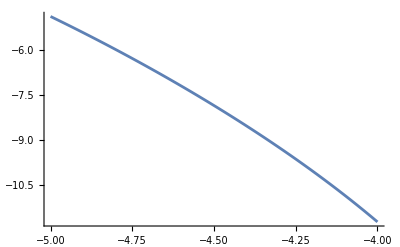

```mathematica
Plot[f'[x], {x,-5,-4}]
```

Извод: (1) Първата производна има стойности между -5 и -12. Следователно те са изцяло отрицателни и f’(x) < 0 за целия интервал [-5; -4].

### Проверка на знака на втората производна.

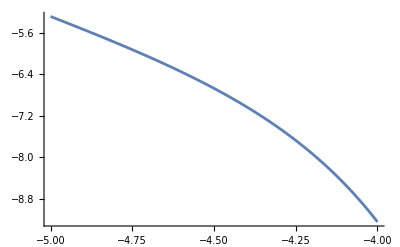

```mathematica
Plot[f''[x], {x,-5,-4}]
```

Извод: (2) Втората производна има стойности между -5 и -9. Следователно те са изцяло отрицателни и f’’(x) < 0 за целия интервал [-5; -4].

Отговор: От (1) и (2) следва, че са изпълнени условията на метода на хордите (първата и втората производна имат постоянен знак в целия интервал [-5;-4].)